# Singular Trimer

## Rigid motions

```mathematica
(T={Subscript[x, 1],Subscript[y, 1]}~Join~(RotationMatrix[ϕ].{Subscript[q, 1],0}+{Subscript[x, 1],Subscript[y, 1]})~Join~(RotationMatrix[ϕ].{Subscript[q, 2],Subscript[q, 3]}+{Subscript[x, 1],Subscript[y, 1]})~Join~(RotationMatrix[ϕ].{Subscript[q, 4],Subscript[q, 5]}+{Subscript[x, 1],Subscript[y, 1]}))//MatrixForm
```

(x_1
y_1
Cos[ϕ] q_1+x_1
Sin[ϕ] q_1+y_1
Cos[ϕ] q_2-Sin[ϕ] q_3+x_1
Sin[ϕ] q_2+Cos[ϕ] q_3+y_1
Cos[ϕ] q_4-Sin[ϕ] q_5+x_1
Sin[ϕ] q_4+Cos[ϕ] q_5+y_1)

```mathematica
D[T,{{Subscript[x, 1],Subscript[y, 1],ϕ,Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5]}}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | -Sin[ϕ] q_1 | Cos[ϕ] | 0 | 0 | 0 | 0
0 | 1 | Cos[ϕ] q_1 | Sin[ϕ] | 0 | 0 | 0 | 0
1 | 0 | -Sin[ϕ] q_2-Cos[ϕ] q_3 | 0 | Cos[ϕ] | -Sin[ϕ] | 0 | 0
0 | 1 | Cos[ϕ] q_2-Sin[ϕ] q_3 | 0 | Sin[ϕ] | Cos[ϕ] | 0 | 0
1 | 0 | -Sin[ϕ] q_4-Cos[ϕ] q_5 | 0 | 0 | 0 | Cos[ϕ] | -Sin[ϕ]
0 | 1 | Cos[ϕ] q_4-Sin[ϕ] q_5 | 0 | 0 | 0 | Sin[ϕ] | Cos[ϕ])

```mathematica
D[T,{{Subscript[x, 1],Subscript[y, 1],ϕ,Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5]}}]//Det//Abs//Simplify
```

Abs[q_1]

## Constraint map

The constraint map is defined the conventional way using difference of length^2of the springs. I’ve not included the natural lengths of the springs since they don’t affect the computation of the Jacobian or the Hessian. There are 4 particles in 2D with 5 DOF and 4 constraints.

```mathematica
fsq=({{Subscript[q, 1]^2}, {(Subscript[q, 2]-Subscript[q, 1])^2+Subscript[q, 3]^2}, {Subscript[q, 2]^2+Subscript[q, 3]^2}, {Subscript[q, 4]^2+Subscript[q, 5]^2}});
ϕ={Subscript[q, 1]->a,Subscript[q, 2]->1/2 a,Subscript[q, 3]->0,Subscript[q, 4]->a Cos[θ],Subscript[q, 5]->a Sin[θ]};
```

```mathematica
length=Simplify[fsq/.ϕ//Sqrt,a>0];
```

```mathematica
f=fsq/(2length);
```

```mathematica
length
```

{{a},{a/2},{a/2},{a}}

## Various matrices

### Jacobians

These are the Jacobians at the collinear (self-stressed) state.

```mathematica
(J=Flatten[Transpose@D[f,{{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5]}}]/.ϕ,1]//Simplify)//MatrixForm
```

(1 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | Cos[θ] | Sin[θ])

```mathematica
(Dyn=κ Transpose@J.J//Simplify)//MatrixForm
```

(2 κ | -κ | 0 | 0 | 0
-κ | 2 κ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | κ Cos[θ]^2 | κ Cos[θ] Sin[θ]
0 | 0 | 0 | κ Cos[θ] Sin[θ] | κ Sin[θ]^2)

```mathematica
Dyn//Eigenvectors//Simplify
```

{{-1,1,0,0,0},{0,0,0,Cot[θ],1},{1,1,0,0,0},{0,0,0,-Tan[θ],1},{0,0,1,0,0}}

```mathematica
DetDPerp=Fold[Times,Part[Dyn//Eigenvalues//Simplify,1;;3]]
```

3 κ^3

```mathematica
G=D[Table[Subscript[q, i],{i,5}]/.ϕ,θ].D[Table[Subscript[q, i],{i,5}]/.ϕ,θ]//FullSimplify
```

a^2

### Self stresses

```mathematica
σ=Normalize/@NullSpace[Transpose@J]//Simplify//Flatten
```

{-1/(√3),1/(√3),1/(√3),0}

### List of Hessians of each constraint

```mathematica
MatrixForm/@(H=Flatten[Transpose@D[f,{{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5]},2}],1])
```

{(1/a | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(2/a | -2/a | 0 | 0 | 0
-2/a | 2/a | 0 | 0 | 0
0 | 0 | 2/a | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 2/a | 0 | 0 | 0
0 | 0 | 2/a | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/a | 0
0 | 0 | 0 | 0 | 1/a)}

## Energy

Take the singular zero mode to be

```mathematica
u={0,0,Subscript[q, 3],0,0};
```

and compute the w vector as

```mathematica
(w=1/2 H.u.u)//MatrixForm
```

(0
q_3^2/a
q_3^2/a
0)

The term in the exponential is

```mathematica
1/2(σ.w)^2
```

(2 q_3^4)/(3 a^2)

```mathematica
P=(((2π)/β)^(3/2)√G)/(√DetDPerp)Integrate[Exp[-1/2 β κ(σ.w)^2],{Subscript[q, 3],-∞,∞},Assumptions->{a>0,β>0,κ>0}]//Simplify//FullSimplify
```

((2/3)^(1/4) √a √(a^2) π^(3/2) (1/β)^(3/2) Gamma[1/4])/((β κ)^(1/4) √(κ^3))

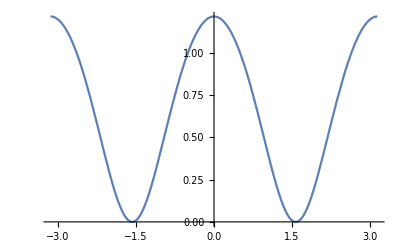

```mathematica
Plot[7/4Log[1+Cos[t]^2],{t,-π,π}]
```